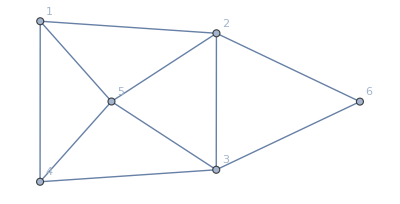

```mathematica
g=Graph[{1<->2,2<->3,3<->4,4<->1,1<->5,2<->5,3<->5,4<->5,2<->6,3<->6}, VertexLabels->Automatic]
```

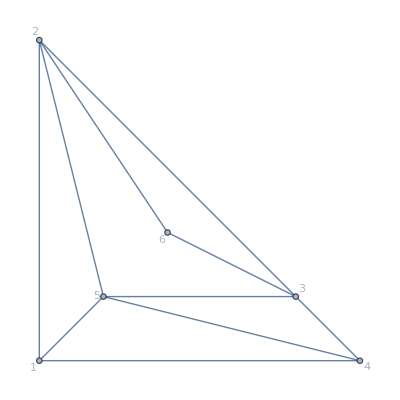
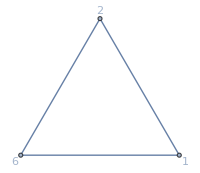
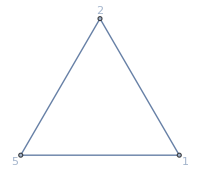
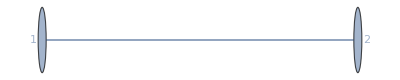
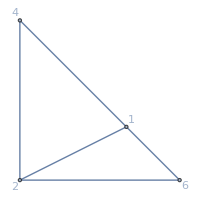
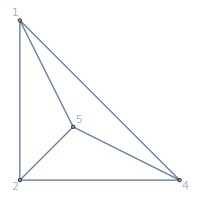
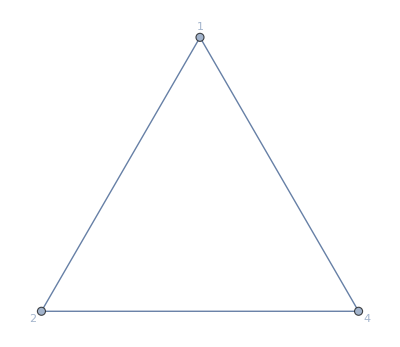
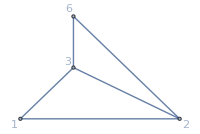
-Graphics-{(-2+x)^2 (7-5 x+x^2),144}
13♁24 | -Graphics-{-2+x,24} | -Graphics-{-2+x,24} | -Graphics-{1,12} | (-2+x)^2
13♁2♁4 | -Graphics-{(-2+x)^2,48} | -Graphics-{(-3+x) (-2+x),24} | -Graphics-{-2+x,24} | (-3+x) (-2+x)^2
1♁24♁3 | -Graphics-{(-2+x)^2,48} | -Graphics-{(-3+x) (-2+x),24} | -Graphics-{-2+x,24} | (-3+x) (-2+x)^2
1♁2♁3♁4 | -Graphics-{(-3+x) (-2+x)^2,48} | -Graphics-{(-4+x) (-3+x) (-2+x),0} | -Graphics-{(-3+x) (-2+x),24} | (-4+x) (-3+x) (-2+x)^2

```mathematica
ZykovDecomposition[g,{1,2,3,4}]
```

```mathematica
AnnotationValue[g,"VertexLabels"]
```

$Failed

```mathematica
PropertyValue[g]
```

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

PropertyValue[-Graphics-]

```mathematica
ApplyToGraph[g_Graph,sets_List]:=Block[{result=g, labels},
labels=AnnotationValue[g,"VertexLabels"];
If [FailureQ[labels],
labels=Map[#->#&,VertexList[g]]
];
labels=Association[labels];
Table[
If[Length[bucket]≠1,
labels[bucket[[1]]]=ToString[labels[bucket[[1]]]]<>", " <> ToString[bucket[[2]]];
labels=KeyDrop[labels,bucket[[2]]];
result=Graph[VertexContract[result,bucket],VertexLabels->Normal[labels]]
],
{bucket,sets}
];
result
]
```

```mathematica
SymbolToGraph[s_]:=Block[{blocks=SymbolToSets[s]},
CompleteGraph[Length[blocks],VertexLabels->Table[k->If[Length[blocks[[k]]]==1,ToString[blocks[[k,1]]],StringRiffle[Map[ToString,blocks[[k]]],", "]],{k,Length[blocks]}], ImageSize->120, VertexStyle->Red, VertexLabelStyle->Darker[Green], EdgeStyle->Darker[Green], VertexSize->Small]
]
```

```mathematica
GraphWithChrom[g_]:=Block[{isPlanar=PlanarGraphQ[g], colofour = ChromaticPolynomial[g,4]},
Labeled[If[isPlanar,Graph[g,GraphLayout->"PlanarEmbedding"],g],
Style[{Factor[ChromaticPolynomial[g,x]/(x(x-1))],colofour},If[colofour!=0,Darker[Green],Red],If[isPlanar,Underlined,Italic]]]
]
```

```mathematica
ZykovDecomposition[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta,g2},
g2=Graph[g,VertexLabels->Map[#->#&,VertexList[g]]];
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g2,split[[1]]];
right=VertexDelete[g2,split[[2]]];
middle=VertexDelete[g2,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
Column[
{GraphWithChrom[Graph[EdgeList[g2],GraphHighlight->EdgeList[CycleGr[vertices]],GraphHighlightStyle->"Thick", GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->400]],
Row[Map[SymbolToGraph,FindFullFormula[middle]]//Reverse,"       "],
TableForm[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
{Rotate[SetsToLabel[sol],Pi/2],GraphWithChrom[lefta]*GraphWithChrom[righta]/GraphWithChrom[middlea],Rotate[Framed[TraditionalForm[Factor[(ChromaticPolynomial[lefta,x]*ChromaticPolynomial[righta,x]/ChromaticPolynomial[middlea,x])/(x(x-1))]]],-Pi/2]},
{sol,sols}
]
]
}
]
]
```

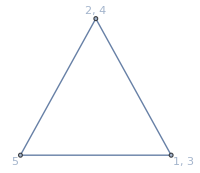
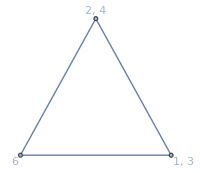
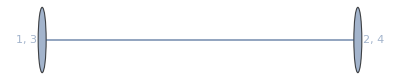
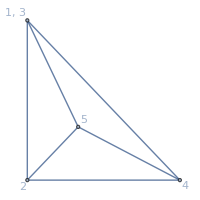
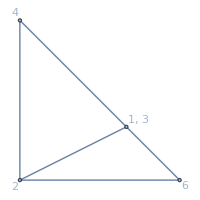
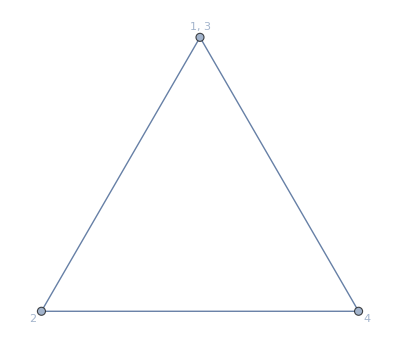
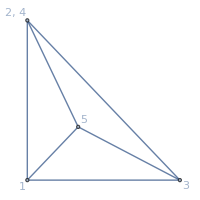
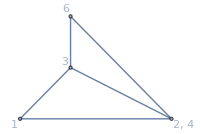
-Graphics-{(-2+x)^2 (7-5 x+x^2),144}
              -Graphics--Graphics--Graphics--Graphics-
13♁24 | (-Graphics-{-2+x,24} -Graphics-{-2+x,24})/(-Graphics-{1,12}) | (x-2)^2
13♁2♁4 | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-2+x)^2,48})/(-Graphics-{-2+x,24}) | (x-3) (x-2)^2
1♁24♁3 | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-2+x)^2,48})/(-Graphics-{-2+x,24}) | (x-3) (x-2)^2
1♁2♁3♁4 | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x)^2,48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2)^2

```mathematica
ZykovDecomposition[g,{1,2,3,4}]
```

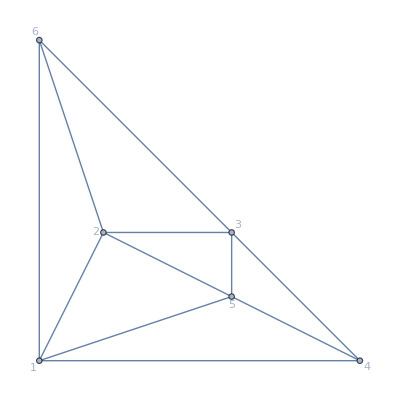

```mathematica
h=Graph[{1<->2,2<->3,3<->4,4<->1,1<->5,2<->5,3<->5,4<->5,2<->6,3<->6,1<->6}, VertexLabels->Automatic, GraphLayout->"PlanarEmbedding"]
```

```mathematica
MaximalPlanarQ[h]
```

False

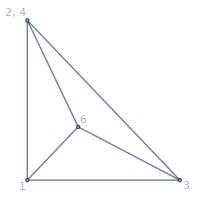
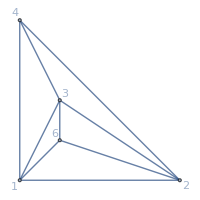
-Graphics-{(-2+x) (-23+23 x-8 x^2+x^3),120}
              -Graphics--Graphics--Graphics--Graphics-
13♁24 | (-Graphics-{-2+x,24} -Graphics-{-2+x,24})/(-Graphics-{1,12}) | (x-2)^2
13♁2♁4 | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-2+x)^2,48})/(-Graphics-{-2+x,24}) | (x-3) (x-2)^2
1♁24♁3 | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-3+x) (-2+x),24})/(-Graphics-{-2+x,24}) | (x-3)^2 (x-2)
1♁2♁3♁4 | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x)^2 (-2+x),24})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3)^2 (x-2)

```mathematica
ZykovDecomposition[h,{1,2,3,4}]
```

```mathematica
h
```

-Graphics-

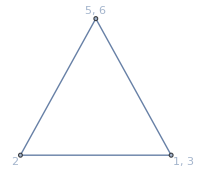
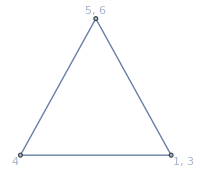
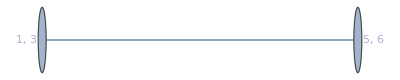
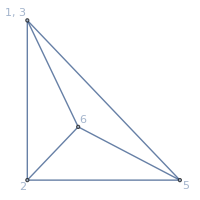
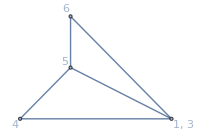
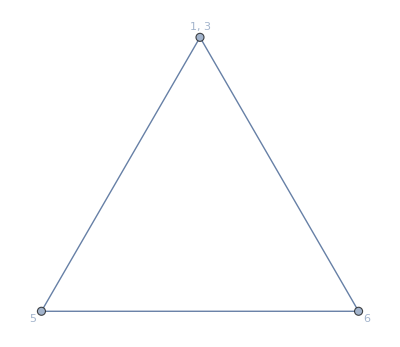
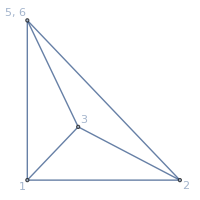
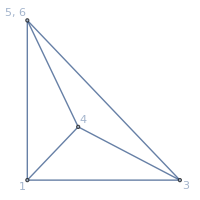
-Graphics-{(-2+x) (-23+23 x-8 x^2+x^3),120}
              -Graphics--Graphics--Graphics--Graphics-
13♁56 | (-Graphics-{-2+x,24} -Graphics-{-2+x,24})/(-Graphics-{1,12}) | (x-2)^2
13♁5♁6 | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-2+x)^2,48})/(-Graphics-{-2+x,24}) | (x-3) (x-2)^2
1♁3♁56 | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-3+x) (-2+x),24})/(-Graphics-{-2+x,24}) | (x-3)^2 (x-2)
1♁3♁5♁6 | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x)^2 (-2+x),24})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3)^2 (x-2)

```mathematica
ZykovDecomposition[h,{1,6,3,5}]
```

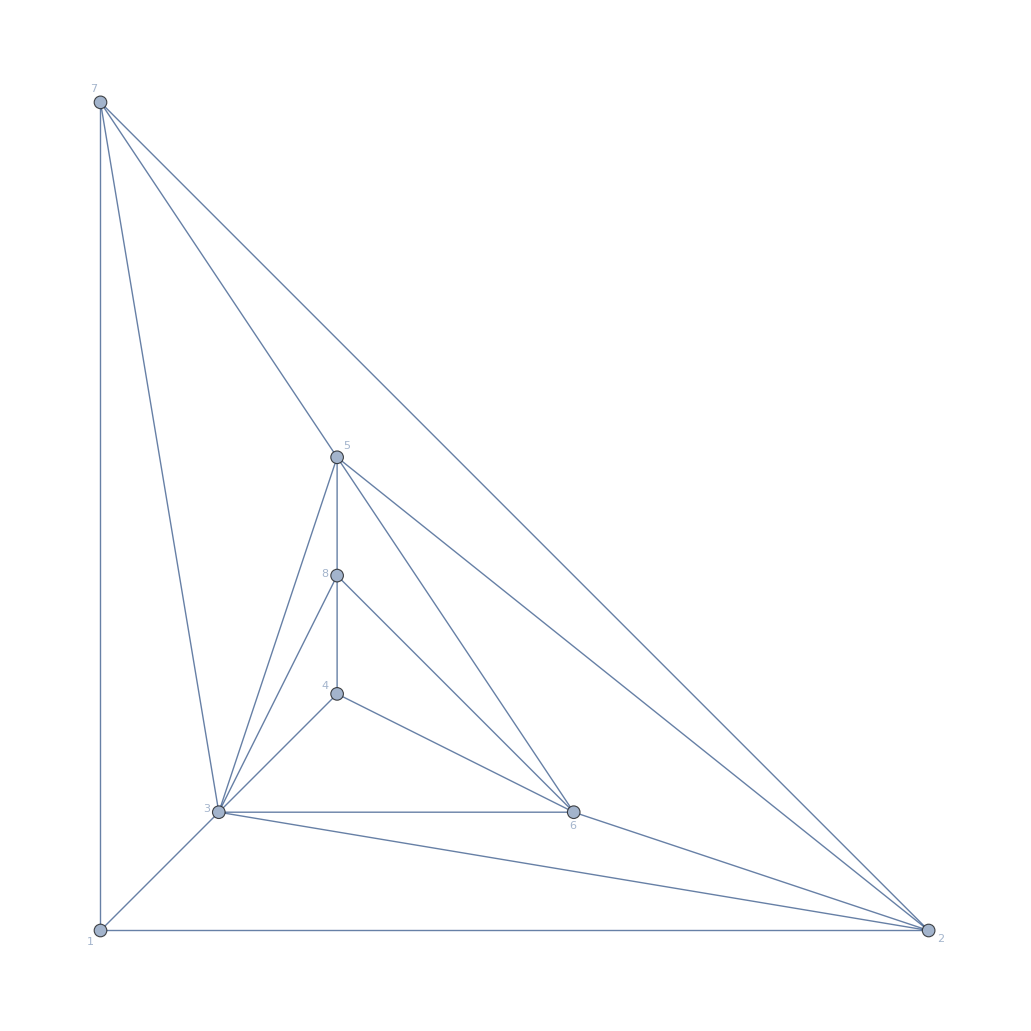

```mathematica
j=Graph[ReadGrof[12], VertexLabels->Automatic, GraphLayout->"PlanarEmbedding"]
```

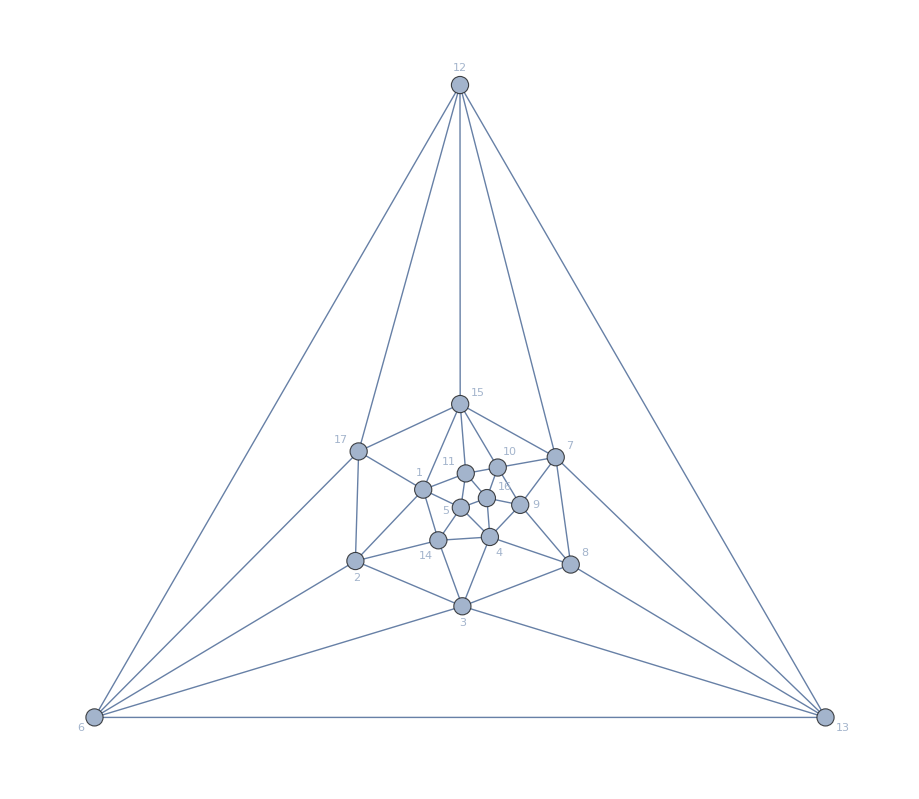

```mathematica
plantri8
```

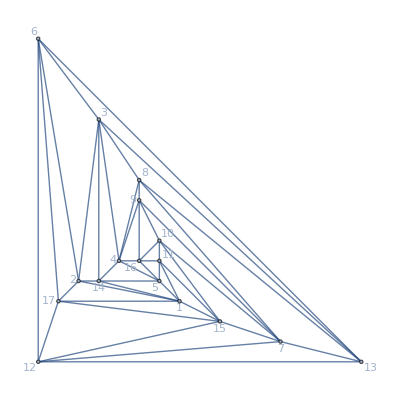
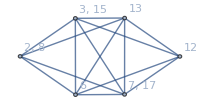
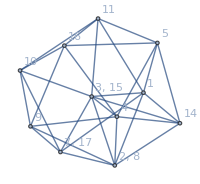
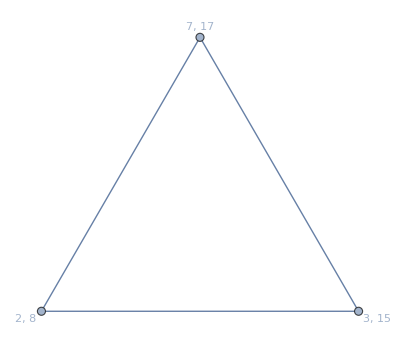
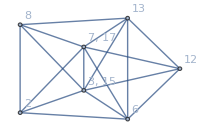
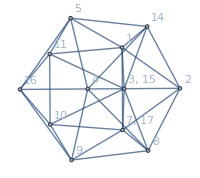
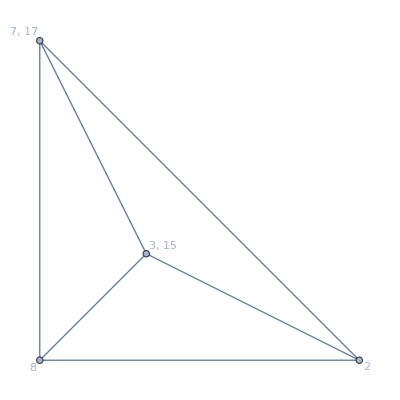
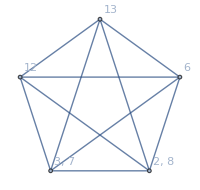
-Graphics-{(-3+x) (-2+x) (-11877662+36882093 x-54248780 x^2+50261369 x^3-32818907 x^4+15966933 x^5-5952318 x^6+1718826 x^7-383596 x^8+65179 x^9-8175 x^10+715 x^11-39 x^12+x^13),528}
              -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
28♁3f♁7h | (-Graphics-{(-4+x)^2 (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (-12446+20308 x-14639 x^2+6081 x^3-1578 x^4+256 x^5-24 x^6+x^7),48})/(-Graphics-{-2+x,24}) | (x-4)^2 (x-3)^2 (x-2) (x^7-24 x^6+256 x^5-1578 x^4+6081 x^3-14639 x^2+20308 x-12446)
2♁3f♁7h♁8 | (-Graphics-{(-4+x) (-3+x) (-2+x) (13-7 x+x^2),0} -Graphics-{(-3+x) (-2+x) (43390-81259 x+68571 x^2-34194 x^3+11047 x^4-2369 x^5+329 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-7 x+13) (x^8-27 x^7+329 x^6-2369 x^5+11047 x^4-34194 x^3+68571 x^2-81259 x+43390)
28f♁37h | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (3318-4705 x+2865 x^2-966 x^3+191 x^4-21 x^5+x^6),48})/(-Graphics-{1,12}) | (x-4) (x-3)^2 (x-2)^2 (x^6-21 x^5+191 x^4-966 x^3+2865 x^2-4705 x+3318)
2♁37h♁8f | (-Graphics-{(-3+x) (-2+x) (10-6 x+x^2),48} -Graphics-{(-3+x) (-2+x) (-11142+18794 x-13934 x^2+5915 x^3-1558 x^4+255 x^5-24 x^6+x^7),48})/(-Graphics-{-2+x,24}) | (x-3)^2 (x-2) (x^2-6 x+10) (x^7-24 x^6+255 x^5-1558 x^4+5915 x^3-13934 x^2+18794 x-11142)
28f♁3♁7h | (-Graphics-{(-4+x)^2 (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (-9126+15542 x-11727 x^2+5103 x^3-1386 x^4+235 x^5-23 x^6+x^7),48})/(-Graphics-{-2+x,24}) | (x-4)^2 (x-3)^2 (x-2) (x^7-23 x^6+235 x^5-1386 x^4+5103 x^3-11727 x^2+15542 x-9126)
2♁3♁7h♁8f | (-Graphics-{(-3+x) (-2+x) (-55+42 x-11 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (42542-80227 x+68054 x^2-34060 x^3+11029 x^4-2368 x^5+329 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-11 x^2+42 x-55) (x^8-27 x^7+329 x^6-2368 x^5+11029 x^4-34060 x^3+68054 x^2-80227 x+42542)
2f♁37h♁8 | (-Graphics-{(-3+x) (-2+x) (10-6 x+x^2),48} -Graphics-{(-3+x) (-2+x) (-9366+15874 x-11895 x^2+5140 x^3-1389 x^4+235 x^5-23 x^6+x^7),48})/(-Graphics-{-2+x,24}) | (x-3)^2 (x-2) (x^2-6 x+10) (x^7-23 x^6+235 x^5-1389 x^4+5140 x^3-11895 x^2+15874 x-9366)
2f♁3♁7h♁8 | (-Graphics-{(-3+x) (-2+x) (-55+42 x-11 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (36166-68433 x+58408 x^2-29546 x^3+9728 x^4-2138 x^5+306 x^6-26 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-11 x^2+42 x-55) (x^8-26 x^7+306 x^6-2138 x^5+9728 x^4-29546 x^3+58408 x^2-68433 x+36166)
28♁37h♁f | (-Graphics-{(-3+x) (-2+x) (10-6 x+x^2),48} -Graphics-{(-4+x) (-3+x) (-2+x) (3028-4200 x+2537 x^2-863 x^3+175 x^4-20 x^5+x^6),0})/(-Graphics-{-2+x,24}) | (x-4) (x-3)^2 (x-2) (x^2-6 x+10) (x^6-20 x^5+175 x^4-863 x^3+2537 x^2-4200 x+3028)
2♁37h♁8♁f | (-Graphics-{(-3+x) (-2+x) (-34+29 x-9 x^2+x^3),48} -Graphics-{(-4+x) (-3+x) (-2+x) (-10597+17222 x-12499 x^2+5282 x^3-1407 x^4+236 x^5-23 x^6+x^7),0})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^3-9 x^2+29 x-34) (x^7-23 x^6+236 x^5-1407 x^4+5282 x^3-12499 x^2+17222 x-10597)
28♁3♁7h♁f | (-Graphics-{(-4+x) (-3+x) (-2+x) (14-7 x+x^2),0} -Graphics-{(-3+x) (-2+x) (46050-84812 x+70489 x^2-34717 x^3+11119 x^4-2373 x^5+329 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-7 x+14) (x^8-27 x^7+329 x^6-2373 x^5+11119 x^4-34717 x^3+70489 x^2-84812 x+46050)
2♁3♁7h♁8♁f | (-Graphics-{(-4+x)^2 (-3+x) (-2+x) (15-7 x+x^2),0} -Graphics-{(-4+x) (-3+x) (-2+x) (52102-92701 x+74835 x^2-36029 x^3+11351 x^4-2396 x^5+330 x^6-27 x^7+x^8),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4)^2 (x-3) (x-2) (x^2-7 x+15) (x^8-27 x^7+330 x^6-2396 x^5+11351 x^4-36029 x^3+74835 x^2-92701 x+52102)
28f♁37♁h | (-Graphics-{(-4+x)^2 (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (-8204+14440 x-11189 x^2+4967 x^3-1368 x^4+234 x^5-23 x^6+x^7),96})/(-Graphics-{-2+x,24}) | (x-4)^2 (x-3)^2 (x-2) (x^7-23 x^6+234 x^5-1368 x^4+4967 x^3-11189 x^2+14440 x-8204)
2♁37♁8f♁h | (-Graphics-{(-3+x) (-2+x) (-55+42 x-11 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (38253-74307 x+64586 x^2-32944 x^3+10819 x^4-2346 x^5+328 x^6-27 x^7+x^8),24})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-11 x^2+42 x-55) (x^8-27 x^7+328 x^6-2346 x^5+10819 x^4-32944 x^3+64586 x^2-74307 x+38253)
2f♁37♁8h | (-Graphics-{(-4+x)^2 (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (-10295+16987 x-12439 x^2+5277 x^3-1407 x^4+236 x^5-23 x^6+x^7),120})/(-Graphics-{-2+x,24}) | (x-4)^2 (x-3)^2 (x-2) (x^7-23 x^6+236 x^5-1407 x^4+5277 x^3-12439 x^2+16987 x-10295)
2f♁37♁8♁h | (-Graphics-{(-4+x) (-3+x) (-2+x) (14-7 x+x^2),0} -Graphics-{(-3+x) (-2+x) (33523-64284 x+55708 x^2-28601 x^3+9538 x^4-2117 x^5+305 x^6-26 x^7+x^8),72})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-7 x+14) (x^8-26 x^7+305 x^6-2117 x^5+9538 x^4-28601 x^3+55708 x^2-64284 x+33523)
2♁37♁8h♁f | (-Graphics-{(-4+x) (-3+x) (-2+x) (13-7 x+x^2),0} -Graphics-{(-3+x) (-2+x) (45175-83753 x+69963 x^2-34582 x^3+11101 x^4-2372 x^5+329 x^6-27 x^7+x^8),72})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-7 x+13) (x^8-27 x^7+329 x^6-2372 x^5+11101 x^4-34582 x^3+69963 x^2-83753 x+45175)
28♁37♁f♁h | (-Graphics-{(-3+x) (-2+x) (-55+42 x-11 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (41638-78813 x+67005 x^2-33600 x^3+10909 x^4-2351 x^5+328 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-11 x^2+42 x-55) (x^8-27 x^7+328 x^6-2351 x^5+10909 x^4-33600 x^3+67005 x^2-78813 x+41638)
2♁37♁8♁f♁h | (-Graphics-{(-4+x)^2 (-3+x) (-2+x) (15-7 x+x^2),0} -Graphics-{(-4+x) (-3+x) (-2+x) (47813-86781 x+71367 x^2-34913 x^3+11141 x^4-2374 x^5+329 x^6-27 x^7+x^8),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4)^2 (x-3) (x-2) (x^2-7 x+15) (x^8-27 x^7+329 x^6-2374 x^5+11141 x^4-34913 x^3+71367 x^2-86781 x+47813)
27♁3f♁8h | (-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (-13084+21120 x-15070 x^2+6200 x^3-1595 x^4+257 x^5-24 x^6+x^7),96})/(-Graphics-{-2+x,24}) | (x-5) (x-4) (x-3)^2 (x-2) (x^7-24 x^6+257 x^5-1595 x^4+6200 x^3-15070 x^2+21120 x-13084)
27♁3f♁8♁h | (-Graphics-{(-4+x) (-3+x) (-2+x) (17-8 x+x^2),0} -Graphics-{(-3+x) (-2+x) (41890-79472 x+67734 x^2-34001 x^3+11025 x^4-2368 x^5+329 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-8 x+17) (x^8-27 x^7+329 x^6-2368 x^5+11025 x^4-34001 x^3+67734 x^2-79472 x+41890)
27♁3h♁8f | (-Graphics-{(-4+x)^2 (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (-12236+20088 x-14553 x^2+6066 x^3-1577 x^4+256 x^5-24 x^6+x^7),96})/(-Graphics-{-2+x,24}) | (x-4)^2 (x-3)^2 (x-2) (x^7-24 x^6+256 x^5-1577 x^4+6066 x^3-14553 x^2+20088 x-12236)
27♁3♁8f♁h | (-Graphics-{(-3+x) (-2+x) (-71+50 x-12 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (41042-78440 x+67217 x^2-33867 x^3+11007 x^4-2367 x^5+329 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-12 x^2+50 x-71) (x^8-27 x^7+329 x^6-2367 x^5+11007 x^4-33867 x^3+67217 x^2-78440 x+41042)
27♁3h♁8♁f | (-Graphics-{(-4+x) (-3+x) (-2+x) (13-7 x+x^2),0} -Graphics-{(-3+x) (-2+x) (45670-84461 x+70369 x^2-34699 x^3+11118 x^4-2373 x^5+329 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-7 x+13) (x^8-27 x^7+329 x^6-2373 x^5+11118 x^4-34699 x^3+70369 x^2-84461 x+45670)
27♁3♁8h♁f | (-Graphics-{(-4+x) (-3+x) (-2+x) (17-8 x+x^2),0} -Graphics-{(-3+x) (-2+x) (47964-87886 x+72594 x^2-35505 x^3+11289 x^4-2393 x^5+330 x^6-27 x^7+x^8),96})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-8 x+17) (x^8-27 x^7+330 x^6-2393 x^5+11289 x^4-35505 x^3+72594 x^2-87886 x+47964)
27♁3♁8♁f♁h | (-Graphics-{(-4+x)^2 (-3+x) (-2+x) (19-8 x+x^2),0} -Graphics-{(-4+x) (-3+x) (-2+x) (50602-90914 x+73998 x^2-35836 x^3+11329 x^4-2395 x^5+330 x^6-27 x^7+x^8),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4)^2 (x-3) (x-2) (x^2-8 x+19) (x^8-27 x^7+330 x^6-2395 x^5+11329 x^4-35836 x^3+73998 x^2-90914 x+50602)
2♁3f♁7♁8h | (-Graphics-{(-4+x) (-3+x) (-2+x) (17-8 x+x^2),0} -Graphics-{(-3+x) (-2+x) (43094-80761 x+68249 x^2-34092 x^3+11031 x^4-2368 x^5+329 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-8 x+17) (x^8-27 x^7+329 x^6-2368 x^5+11031 x^4-34092 x^3+68249 x^2-80761 x+43094)
28♁3f♁7♁h | (-Graphics-{(-3+x) (-2+x) (-71+50 x-12 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (39557-75821 x+65291 x^2-33110 x^3+10839 x^4-2347 x^5+328 x^6-27 x^7+x^8),24})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-12 x^2+50 x-71) (x^8-27 x^7+328 x^6-2347 x^5+10839 x^4-33110 x^3+65291 x^2-75821 x+39557)
2♁3f♁7♁8♁h | (-Graphics-{(-4+x)^2 (-3+x) (-2+x) (19-8 x+x^2),0} -Graphics-{(-4+x)^2 (-3+x) (-2+x) (-11433+18089 x-12891 x^2+5383 x^3-1422 x^4+237 x^5-23 x^6+x^7),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4)^3 (x-3) (x-2) (x^2-8 x+19) (x^7-23 x^6+237 x^5-1422 x^4+5383 x^3-12891 x^2+18089 x-11433)
28f♁3h♁7 | (-Graphics-{(-4+x)^2 (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (-8421+14614 x-11235 x^2+4971 x^3-1368 x^4+234 x^5-23 x^6+x^7),72})/(-Graphics-{-2+x,24}) | (x-4)^2 (x-3)^2 (x-2) (x^7-23 x^6+234 x^5-1368 x^4+4971 x^3-11235 x^2+14614 x-8421)
2♁3h♁7♁8f | (-Graphics-{(-4+x) (-3+x) (-2+x) (14-7 x+x^2),0} -Graphics-{(-3+x) (-2+x) (40550-76817 x+65666 x^2-33173 x^3+10843 x^4-2347 x^5+328 x^6-27 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^2-7 x+14) (x^8-27 x^7+328 x^6-2347 x^5+10843 x^4-33173 x^3+65666 x^2-76817 x+40550)
28f♁3♁7♁h | (-Graphics-{(-3+x) (-2+x) (-71+50 x-12 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (29597-58203 x+51789 x^2-27264 x^3+9285 x^4-2092 x^5+304 x^6-26 x^7+x^8),24})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-12 x^2+50 x-71) (x^8-26 x^7+304 x^6-2092 x^5+9285 x^4-27264 x^3+51789 x^2-58203 x+29597)
2♁3♁7♁8f♁h | (-Graphics-{(-4+x) (-3+x) (-2+x) (-79+52 x-12 x^2+x^3),0} -Graphics-{(-4+x)^2 (-3+x) (-2+x) (-11221+17884 x-12813 x^2+5369 x^3-1421 x^4+237 x^5-23 x^6+x^7),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4)^2 (x-3) (x-2) (x^3-12 x^2+52 x-79) (x^7-23 x^6+237 x^5-1421 x^4+5369 x^3-12813 x^2+17884 x-11221)
2f♁3h♁7♁8 | (-Graphics-{(-3+x) (-2+x) (-55+42 x-11 x^2+x^3),24} -Graphics-{(-4+x) (-3+x) (-2+x) (-8394+14029 x-10458 x^2+4545 x^3-1249 x^4+217 x^5-22 x^6+x^7),0})/(-Graphics-{(-3+x) (-2+x),24}) | (x-4) (x-3) (x-2) (x^3-11 x^2+42 x-55) (x^7-22 x^6+217 x^5-1249 x^4+4545 x^3-10458 x^2+14029 x-8394)
2f♁3♁7♁8h | (-Graphics-{(-3+x) (-2+x) (-71+50 x-12 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (35870-67935 x+58086 x^2-29444 x^3+9712 x^4-2137 x^5+306 x^6-26 x^7+x^8),48})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-12 x^2+50 x-71) (x^8-26 x^7+306 x^6-2137 x^5+9712 x^4-29444 x^3+58086 x^2-67935 x+35870)
2f♁3♁7♁8♁h | (-Graphics-{(-4+x) (-3+x) (-2+x) (-79+52 x-12 x^2+x^3),0} -Graphics-{(-4+x)^2 (-3+x) (-2+x) (-9627+15334 x-11039 x^2+4684 x^3-1267 x^4+218 x^5-22 x^6+x^7),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4)^2 (x-3) (x-2) (x^3-12 x^2+52 x-79) (x^7-22 x^6+218 x^5-1267 x^4+4684 x^3-11039 x^2+15334 x-9627)
28♁3h♁7♁f | (-Graphics-{(-3+x) (-2+x) (-55+42 x-11 x^2+x^3),24} -Graphics-{(-3+x) (-2+x) (43337-80810 x+67926 x^2-33808 x^3+10932 x^4-2352 x^5+328 x^6-27 x^7+x^8),24})/(-Graphics-{(-3+x) (-2+x),24}) | (x-3) (x-2) (x^3-11 x^2+42 x-55) (x^8-27 x^7+328 x^6-2352 x^5+10932 x^4-33808 x^3+67926 x^2-80810 x+43337)
2♁3h♁7♁8♁f | (-Graphics-{(-4+x)^2 (-3+x) (-2+x) (15-7 x+x^2),0} -Graphics-{(-4+x)^2 (-3+x) (-2+x) (-12378+19100 x-13297 x^2+5456 x^3-1427 x^4+237 x^5-23 x^6+x^7),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4)^3 (x-3) (x-2) (x^2-7 x+15) (x^7-23 x^6+237 x^5-1427 x^4+5456 x^3-13297 x^2+19100 x-12378)
2♁3♁7♁8h♁f | (-Graphics-{(-4+x)^2 (-3+x) (-2+x) (19-8 x+x^2),0} -Graphics-{(-4+x) (-3+x) (-2+x) (51806-92203 x+74513 x^2-35927 x^3+11335 x^4-2395 x^5+330 x^6-27 x^7+x^8),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4)^2 (x-3) (x-2) (x^2-8 x+19) (x^8-27 x^7+330 x^6-2395 x^5+11335 x^4-35927 x^3+74513 x^2-92203 x+51806)
28♁3♁7♁f♁h | (-Graphics-{(-4+x) (-3+x) (-2+x) (-79+52 x-12 x^2+x^3),0} -Graphics-{(-4+x) (-3+x) (-2+x) (48269-87263 x+71555 x^2-34945 x^3+11143 x^4-2374 x^5+329 x^6-27 x^7+x^8),0})/(-Graphics-{(-4+x) (-3+x) (-2+x),0}) | (x-4) (x-3) (x-2) (x^3-12 x^2+52 x-79) (x^8-27 x^7+329 x^6-2374 x^5+11143 x^4-34945 x^3+71555 x^2-87263 x+48269)
2♁3♁7♁8♁f♁h | (-Graphics-{(-5+x) (-4+x)^2 (-3+x) (-2+x) (21-8 x+x^2),0} -Graphics-{(-5+x) (-4+x)^2 (-3+x) (-2+x) (-13611+20405 x-13878 x^2+5595 x^3-1445 x^4+238 x^5-23 x^6+x^7),0})/(-Graphics-{(-5+x) (-4+x) (-3+x) (-2+x),0}) | (x-5) (x-4)^3 (x-3) (x-2) (x^2-8 x+21) (x^7-23 x^6+238 x^5-1445 x^4+5595 x^3-13878 x^2+20405 x-13611)

```mathematica
ZykovDecomposition[plantri8,{2,3,8,7,15,17}]
```

```mathematica
ZykovDecomposition[j,{5,6,10,3}]
```

VertexDelete::inv: The argument {5,6,10,3} in VertexDelete[Graph[<8>, <18>], {5, 6, 10, 3}] is not a valid vertex.

ConnectedComponents::graph: A graph object is expected at position 1 in ConnectedComponents[VertexDelete[,{5,6,10,3}]].

VertexDelete::inv: The argument VertexDelete[,{5,6,10,3}] in VertexDelete[Graph[<8>, <18>], VertexDelete[Graph[<8>, <18>], {5, 6, 10, 3}]] is not a valid vertex.

Part::partw: Part 2 of ConnectedComponents[VertexDelete[,{5,6,10,3}]] does not exist.

VertexDelete::inv: The argument ConnectedComponents[VertexDelete[,{5,6,10,3}]]⟦2⟧ in VertexDelete[Graph[<8>, <18>], ConnectedComponents[VertexDelete[Graph[<8>, <18>], {5, 6, 10, 3}]][[2]]] is not a valid vertex.

General::stop: Further output of VertexDelete::inv will be suppressed during this calculation.

VertexList::graph: A graph object is expected at position 1 in ….

General::stop: Further output of VertexList::graph will be suppressed during this calculation.

EdgeAdd::graph: A graph object is expected at position 1 in ….

General::stop: Further output of EdgeAdd::graph will be suppressed during this calculation.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[EdgeAdd[EdgeAdd[EdgeAdd[EdgeAdd[EdgeAdd[EdgeAdd[VertexDelete[«2»],TwoWayRule[«2»]],5<->10],5<->3],6<->10],6<->3],10<->3]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

Table::iterb: Iterator … does not have appropriate bounds.

GraphComplement::graph: A graph object is expected at position 1 in ….

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression pos1 cannot be used as a part specification.

Part::pkspec1: The expression pos2 cannot be used as a part specification.

Part::pkspec1: The expression pos1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

GraphComplement::graph: A graph object is expected at position 1 in ….

Set::pkspec1: The expression pos1 cannot be used as a part specification.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

GraphComplement::graph: A graph object is expected at position 1 in ….

General::stop: Further output of GraphComplement::graph will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

General::stop: Further output of Set::pkspec1 will be suppressed during this calculation.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

General::stop: Further output of Delete::pkspec will be suppressed during this calculation.

$Aborted

```mathematica
SymbolComp3[s1_,s2_]:=Length[SymbolToSets[s1]]<Length[SymbolToSets[s2]]
```

```mathematica
SymbolToSets[v1x25x3x4]
```

{{1},{2,5},{3},{4}}

```mathematica
Sort[FindFullFormula[CycleGraph[5]],SymbolComp3]
```

{v13x24x5,v13x25x4,v14x25x3,v14x2x35,v1x24x35,v13x2x4x5,v14x2x3x5,v1x24x3x5,v1x25x3x4,v1x2x35x4,v1x2x3x4x5}

```mathematica
GraphWithChrom2[g_]:=Labeled[If[PlanarGraphQ[g],Graph[g,GraphLayout->"PlanarEmbedding"],g],Style[{ChromaticPolynomial[g,4]},If[ChromaticPolynomial[g,4]!=0,Darker[Green],Red],Underlined,If[PlanarGraphQ[g],Bold,Underlined]]]
```

```mathematica
ZykovDecomposition2[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta,g2},
g2=Graph[g,VertexLabels->Map[#->#&,VertexList[g]]];
split= ConnectedComponents[VertexDelete[g,vertices]];
left=VertexDelete[g2,split[[1]]];
right=VertexDelete[g2,split[[2]]];
middle=VertexDelete[g2,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Map[SymbolToSets,FindFullFormula[middle]]//Reverse;
Column[
{GraphWithChrom2[Graph[EdgeList[g2],GraphHighlight->EdgeList[CycleGr[vertices]],GraphHighlightStyle->"Thick", GraphLayout->"PlanarEmbedding",VertexLabels->"Name",ImageSize->400]],
Multicolumn[Map[SymbolToGraph,Sort[FindFullFormula[middle],SymbolComp3]]//Reverse],
TableForm[
Monitor[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
{Rotate[SetsToLabel[sol],Pi/2],
GraphWithChrom2[lefta]*GraphWithChrom2[righta]/GraphWithChrom2[middlea]->(Factor[(Framed[ChromaticPolynomial[lefta,4]]*Framed[ChromaticPolynomial[righta,4]]/Framed[ChromaticPolynomial[middlea,4]])])
},
{sol,Select[sols,Length[#]<=4&]}
],
sol]
]
}
]
]
```

```mathematica
ZykovDecomposition2[plantri8,{1,14,4,16,11}]
```

-Graphics-{528}
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
14♁be♁g | (-Graphics-{24} -Graphics-{96})/(-Graphics-{24})→96
1g♁4♁be | (-Graphics-{24} -Graphics-{48})/(-Graphics-{24})→48
1♁4♁be♁g | (-Graphics-{0} -Graphics-{168})/(-Graphics-{24})→(0 168)/24
1g♁4b♁e | (-Graphics-{24} -Graphics-{72})/(-Graphics-{24})→72
1♁4b♁eg | (-Graphics-{24} -Graphics-{144})/(-Graphics-{24})→144
1♁4b♁e♁g | (-Graphics-{0} -Graphics-{192})/(-Graphics-{24})→(0 192)/24
14♁b♁eg | (-Graphics-{24} -Graphics-{168})/(-Graphics-{24})→168
14♁b♁e♁g | (-Graphics-{0} -Graphics-{216})/(-Graphics-{24})→(0 216)/24
1g♁4♁b♁e | (-Graphics-{0} -Graphics-{168})/(-Graphics-{24})→(0 168)/24
1♁4♁b♁eg | (-Graphics-{0} -Graphics-{240})/(-Graphics-{24})→(0 240)/24

```mathematica
ZykovDecomposition2[plantri8,{2,3,8,7,15,17}]
```

```mathematica
Monitor[Table[Mean[VertexDegree[plantri[[k]]]],{k,Length[plantri]}]//Tally//Sort,k]
```

{{5,1},{36/7,1},{26/5,1},{21/4,3},{90/17,4},{16/3,12},{102/19,23},{27/5,73},{38/7,192},{60/11,651},{126/23,2070},{11/2,7290},{138/25,25381},{72/13,64298}}

```mathematica
Length[plantri]
```

100000

```mathematica
Monitor[Table[Min[VertexDegree[Graph[ReadGrof[k]]]],{k,300000}]//Tally//Sort,k]
```

{{3,296942},{4,3056},{5,2}}

```mathematica
ZykovDecomposition2[VertexDelete[plantri8,3],{1,14,4,16,11}]
```

-Graphics-{(-3+x) (-2+x) (1071028-3338692 x+4956105 x^2-4642667 x^3+3056074 x^4-1486219 x^5+545835 x^6-152004 x^7+31746 x^8-4834 x^9+508 x^10-33 x^11+x^12),2784}
              -Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
14♁be♁g | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-3+x) (-2+x) (-45595+107889 x-117669 x^2+77767 x^3-34323 x^4+10478 x^5-2208 x^6+309 x^7-26 x^8+x^9),600})/(-Graphics-{-2+x,24})→600
1g♁4♁be | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-3+x) (-2+x) (-45760+106609 x-115295 x^2+76032 x^3-33641 x^4+10324 x^5-2189 x^6+308 x^7-26 x^8+x^9),480})/(-Graphics-{-2+x,24})→480
1♁4♁be♁g | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (163211-416266 x+497307 x^2-366972 x^3+185068 x^4-66483 x^5+17172 x^6-3138 x^7+387 x^8-29 x^9+x^10),456})/(-Graphics-{(-3+x) (-2+x),24})→(0 456)/24
1g♁4b♁e | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-3+x) (-2+x) (-39235+94702 x-105670 x^2+71556 x^3-32351 x^4+10095 x^5-2166 x^6+307 x^7-26 x^8+x^9),504})/(-Graphics-{-2+x,24})→504
1♁4b♁eg | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-3+x) (-2+x) (-45631+106254 x-114858 x^2+75759 x^3-33551 x^4+10309 x^5-2188 x^6+308 x^7-26 x^8+x^9),600})/(-Graphics-{-2+x,24})→600
1♁4b♁e♁g | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (143636-374020 x+456525 x^2-343919 x^3+176722 x^4-64506 x^5+16874 x^6-3112 x^7+386 x^8-29 x^9+x^10),480})/(-Graphics-{(-3+x) (-2+x),24})→(0 480)/24
14♁b♁eg | (-Graphics-{(-3+x) (-2+x),24} -Graphics-{(-3+x) (-2+x) (-46963+110211 x-119356 x^2+78437 x^3-34476 x^4+10497 x^5-2209 x^6+309 x^7-26 x^8+x^9),600})/(-Graphics-{-2+x,24})→600
14♁b♁e♁g | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (147632-387223 x+473976 x^2-356451 x^3+182175 x^4-65995 x^5+17125 x^6-3136 x^7+387 x^8-29 x^9+x^10),480})/(-Graphics-{(-3+x) (-2+x),24})→(0 480)/24
1g♁4♁b♁e | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (148127-383548 x+465574 x^2-348872 x^3+178394 x^4-64851 x^5+16914 x^6-3114 x^7+386 x^8-29 x^9+x^10),360})/(-Graphics-{(-3+x) (-2+x),24})→(0 360)/24
1♁4♁b♁eg | (-Graphics-{(-4+x) (-3+x) (-2+x),0} -Graphics-{(-3+x) (-2+x) (167315-424600 x+504690 x^2-370669 x^3+186197 x^4-66693 x^5+17194 x^6-3139 x^7+387 x^8-29 x^9+x^10),456})/(-Graphics-{(-3+x) (-2+x),24})→(0 456)/24